## PRACTICAL QUESTIONS PRACTICE :

#### BISECTION METHOD

```mathematica
(*1. Solve cos[x]==0*)
```

1th iteration value is : 1.

Estimated error in 1th iteration is : 1.

2th iteration value is : 1.5

Estimated error in 2th iteration is : 0.5

3th iteration value is : 1.75

Estimated error in 3th iteration is : 0.25

4th iteration value is : 1.625

Estimated error in 4th iteration is : 0.125

5th iteration value is : 1.5625

Estimated error in 5th iteration is : 0.0625

Root is : 1.5625

Estimated error in 6th iteration is : 0.03125

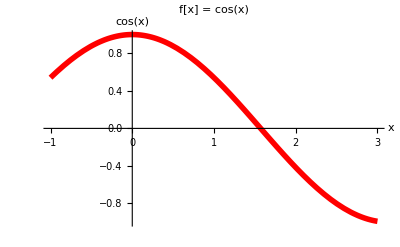

```mathematica
f[x_]:=Cos[x];
x0=0;
x1=2.0;
Nmax=5;
eps=0.0001;
If[N[f[x0] f[x1]]>0,Print["\nYour values do no satisfy the IVP so use new values."],
For[i=1,i<=Nmax,i++,m=(x0+x1)/2;
If[Abs[(x1-x0)/2]<eps,Return[m], Print[i, "th iteration value is : ",m];
Print["Estimated error in ", i, "th iteration is : ", (x1-x0)/2];
If [f[m]*f[x1]<0,x0=m,x1=m]]];
Print["\nRoot is : ",m];
Print["Estimated error in ", i, "th iteration is : ", (x1-x0)/2];];
Print[Plot[f[x],{x,-1,3},PlotRange->{-1,1},PlotStyle->{Red,Thickness[0.01]},PlotLabel->"f[x] = "f[x],AxesLabel->{x,f[x]}]];
```

1th iteration value is 0.25

Estimated error in 1th iteration is : 0.25

2th iteration value is 0.125

Estimated error in 2th iteration is : 0.125

3th iteration value is 0.1875

Estimated error in 3th iteration is : 0.0625

4th iteration value is 0.21875

Estimated error in 4th iteration is : 0.03125

5th iteration value is 0.203125

Estimated error in 5th iteration is : 0.015625

6th iteration value is 0.195313

Estimated error in 6th iteration is : 0.0078125

7th iteration value is 0.199219

Estimated error in 7th iteration is : 0.00390625

8th iteration value is 0.201172

Estimated error in 8th iteration is : 0.00195313

9th iteration value is 0.202148

Estimated error in 9th iteration is : 0.000976563

10th iteration value is 0.20166

Estimated error in 10th iteration is : 0.000488281

11th iteration value is 0.201416

Estimated error in 11th iteration is : 0.000244141

12th iteration value is 0.201538

Estimated error in 12th iteration is : 0.00012207

Return[0.201599]

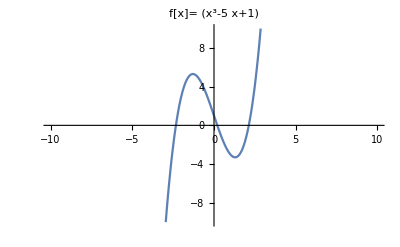

```mathematica
(*Solve x^3-5x+1=0*)
f[x_]:=x^3-5x+1;
x0=0;
x1=0.5;
Nmax=20;
eps=0.0001;
If[N[f[x0]*f[x1]]>0,Print["\nGiven values do not satisfy the IVP, try other values."],For[i=1,i<=Nmax ,i++,m=(x0+x1)/2;If[Abs[(x0-x1)/2]<eps,Return[m],Print[i, "th iteration value is ", m];Print["Estimated error in ",i,"th iteration is : ",(x1-x0)/2];
If[f[m]*f[x1]<0,x0=m,x1=m]]];
Print["\nRoot is : ",m];
Print["Estimated error in ",i,"th iteration is : ",(x1-x0)/2]];
Print[Plot[f[x],{x,-10,10},PlotRange->{-10,10},PlotLabel->"f[x]="f[x]]];
```

1th iteration value is : 0.5

Estimated error in 1th iteration is 1/2

2th iteration value is : 0.75

Estimated error in 2th iteration is 0.25

3th iteration value is : 0.625

Estimated error in 3th iteration is 0.125

4th iteration value is : 0.5625

Estimated error in 4th iteration is 0.0625

5th iteration value is : 0.53125

Estimated error in 5th iteration is 0.03125

6th iteration value is : 0.515625

Estimated error in 6th iteration is 0.015625

7th iteration value is : 0.523438

Estimated error in 7th iteration is 0.0078125

8th iteration value is : 0.519531

Estimated error in 8th iteration is 0.00390625

9th iteration value is : 0.517578

Estimated error in 9th iteration is 0.00195313

10th iteration value is : 0.518555

Estimated error in 10th iteration is 0.000976563

11th iteration value is : 0.518066

Estimated error in 11th iteration is 0.000488281

12th iteration value is : 0.517822

Estimated error in 12th iteration is 0.000244141

13th iteration value is : 0.5177

Estimated error in 13th iteration is 0.00012207

Return[0.517761]

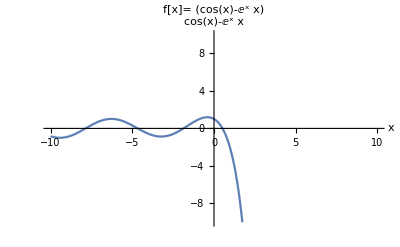

```mathematica
(*Solve cos[x]-xe^x=0*)
f[x_]:=Cos[x]-x*Exp[x];
x0=0;
x1=1;
Nmax=20;
eps=0.0001;
If[N[f[x0]*f[x1]]>0,Print["\nGiven values do not satisfy the IVP try other values"],For[i=1,i<=Nmax,i++,m=N[(x0+x1)/2];
If[Abs[(x0-x1)/2]<eps,Return[m],Print[i,"th iteration value is : ",m];

Print["Estimated error in ",i,"th iteration is ", (x1-x0)/2];
If[f[m]*f[x1]<0,x0=m,x1=m]]];
Print["\nRoot is ",m];
Print["Estimated error in ",i,"th iteration is ", (x1-x0)/2]];
Print[Plot[f[x],{x,-10,10},PlotRange->{-10,10},PlotLabel->"f[x]="f[x],AxesLabel->{x,f[x]}]];
```

Iteration | Left End Point | Approximate Value | Right End Point | Value of func
1 | 1 | 1.5 | 2 | 2.375
2 | 1 | 1.25 | 1.5 | 0.328125
3 | 1 | 1.125 | 1.25 | -0.419922
4 | 1.125 | 1.1875 | 1.25 | -0.067627
5 | 1.1875 | 1.21875 | 1.25 | 0.124725
6 | 1.1875 | 1.20313 | 1.21875 | 0.0271797
7 | 1.1875 | 1.19531 | 1.20313 | -0.0205646
8 | 1.19531 | 1.19922 | 1.20313 | 0.00322217
9 | 1.19531 | 1.19727 | 1.19922 | -0.00869253
10 | 1.19727 | 1.19824 | 1.19922 | -0.00274051

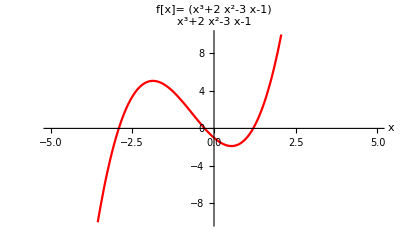

Root after 10 iterations is 1.19824

Accuracy is 0.000488281

```mathematica
(*Solve x^3+2 x^2-3x-1==0*)
f[x_]:=x^3+2 x^2-3x-1;
a=1;
b=2;
Nmax=10;
list={};
If[N[f[a]*f[b]]>=0,Print["\nThe method won't apply in the interval [a,b] for given a,b\nTry new values."],
For[i=1,i<=Nmax,i++,m=N[(a+b)/2];
list=Append[list,{i,a,m,b,f[m]}];
If[f[m]==0,Print["\nExact root of f[x] is ",m],If[f[m]*f[b]<0,a=m,b=m]]];
Print[TableForm[list,TableHeadings->{None,{"Iteration","Left End Point","Approximate Value","Right End Point","Value of func"}}]]];
Print[Plot[f[x],{x,-5,5},PlotRange->{-10,10},PlotLabel->Framed["f[x]="f[x]],AxesLabel->{x,f[x]},PlotStyle->Red]];
Print["\nRoot after ",Nmax," iterations is ", m];Print["\nAccuracy is ", Abs[(b-a)/2]];
```

### REGULA FALSI METHOD

```mathematica
(*Find out root of f[x]=x^3-x-2 in the interval [1,2]*)
```

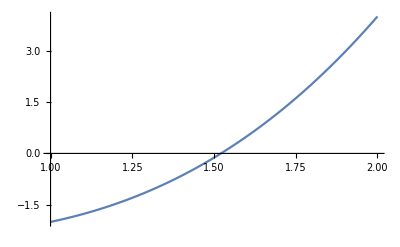

Iteration 0 = 1.33333

Iteration 1 = 1.46269

Iteration 2 = 1.50402

Iteration 3 = 1.51633

Iteration 4 = 1.51992

Iteration 5 = 1.52096

Iteration 6 = 1.52126

Iteration 7 = 1.52134

Iteration 8 = 1.52137

Iteration 9 = 1.52138

Iteration 10 = 1.52138

```mathematica
f[x_]:=x^3-x-2;
a=1;
b=2;
Nmax=10;
Print[Plot[f[x],{x,a,b}]];
For[i=0,i<=Nmax,i++,c=N[(b*f[a]-a*f[b])/(f[a]-f[b])];If[f[c]*f[b]<0,a=c,b=c];Print["Iteration ",i," = ",c]]
```

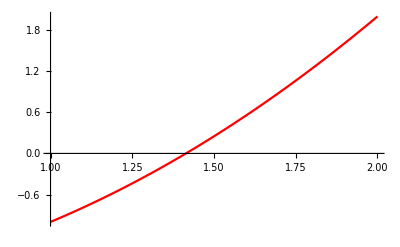

1th Iteration : 1.33333

2th Iteration : 1.4

3th Iteration : 1.41176

4th Iteration : 1.41379

5th Iteration : 1.41414

6th Iteration : 1.4142

7th Iteration : 1.41421

8th Iteration : 1.41421

9th Iteration : 1.41421

10th Iteration : 1.41421

The approximate value of the square root of 2 by Regula Falsi Method after 10 iterations is 1.41421

```mathematica
(*Evaluate square root of 2*)
f[x_]:=x^2-2;
a=1;
b=2;
Nmax=10;
Print[Plot[f[x],{x,a,b},PlotStyle->Red]];
For[i=1,i<=Nmax,i++,c=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
If[f[c]*f[b]<0,a=c,b=c];Print[i,"th Iteration : ",c]];
Print["The approximate value of the square root of 2 by Regula Falsi Method after ",Nmax," iterations is ",c];
```

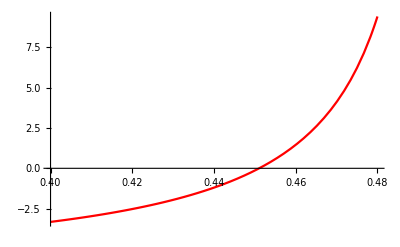

1th iteration : 0.420867

2th iteration : 0.433203

3th iteration : 0.440496

4th iteration : 0.444808

5th iteration : 0.447358

6th iteration : 0.448866

7th iteration : 0.449757

8th iteration : 0.450284

9th iteration : 0.450596

10th iteration : 0.45078

Approximate root of f(x)=-6-x+Tan[π x] after 10 iterations is 0.45078

```mathematica
(*Approximate the root of the equation f[x]= Tan[Pi*x]-x-6 in [0.40,0.48], iterations=10 *)
f[x_]:=Tan[Pi*x]-x-6;
a=0.40;
b=0.48;
Nmax=10;
Print[Plot[f[x],{x,a,b},PlotStyle->Red]];
For[i=1,i<=Nmax,i++,c=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
If[f[c]*f[b]<0,a=c,b=c];Print[i,"th iteration : ",c]];
Print["\nApproximate root of f(x)=",f[x]," after ",Nmax," iterations is ",c];
```

### SECANT METHOD

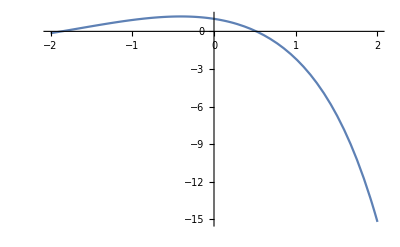

Iteration 1 : 0.314665

Iteration 2 : 0.446728

Iteration 3 : 0.531706

Iteration 4 : 0.516904

Iteration 5 : 0.517747

Iteration 6 : 0.517757

Iteration 7 : 0.517757

Iteration 8 : 0.517757

Iteration 9 : 0.517757

Iteration 10 : 0.517757

```mathematica
(*Solve f[x]=cos[x]-x*e^x*)
f[x_]:=Cos[x]-x*Exp[x];
p0=0;
p1=1;
Nmax=10;
Print[Plot[f[x],{x,-2,2}]];
For[i=1,i<=Nmax,i++,p2=N[(p0*f[p1]-p1*f[p0])/(f[p1]-f[p0])];Print["Iteration ",i," : ",p2];p0=p1;p1=p2;];
```

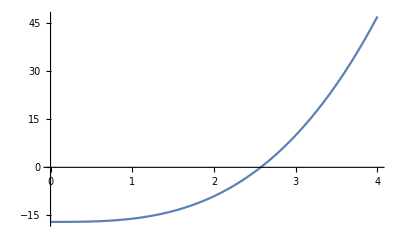

Iteration 1 : 2.473684

Iteration 2 : 2.597352

Iteration 3 : 2.570274

Iteration 4 : 2.571271

Iteration 5 : 2.571282

Iteration 6 : 2.571282

Iteration 7 : 2.571282

Iteration 8 : 2.571282

Iteration 9 : 2.571282

Iteration 10 : 2.571282

```mathematica
(*Find the root of f(x)=x^3-17 taking p0=3,p1=2 after 10 iterations*)
f[x_]:=x^3-17;
p0=3;
p1=2;
Nmax=10;
Print[Plot[f[x],{x,0,4}]];
For[i=1,i<=Nmax,i++,p2=(p1*f[p0]-p0*f[p1])/(f[p0]-f[p1]);Print["Iteration ",i," : ",N[p2,7]];p0=p1;p1=p2;]
```

### NEWTON RAPHSON METHOD

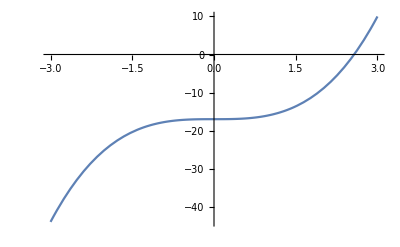

n | p[n] | Error[n]
1 | 2.62963 | 0.05834804
2 | 2.572567 | 0.001285091
3 | 2.571282 | 6.418429×10^-7
4 | 2.571282 | 1.602167×10^-13
5 | 2.571282 | 9.98311×10^-27
6 | 2.571282 | 3.88×10^-53
7 | 2.571282 | 0.
8 | 2.571282 | 0.
9 | 2.571282 | 0.
10 | 2.571282 | 0.

```mathematica
(*Use Newton Raphson Method to find the root of f(x)=x^3-17 taking p_0=3,2 after 10 iterations*)
f[x_]:=x^3-17;
p[0]=3;
Print[Plot[f[x],{x,-3,3}]];
p[n_]:=p[n-1]-f[p[n-1]]/f'[p[n-1]];
err[n_]:= Abs[N[p[n]-CubeRoot[17],7]];
Print[Grid[Prepend[Table[{n,N[p[n],7],err[n]},{n,1,10}],{"n","p[n]","Error[n]"}],Dividers->{{False,True},{False,True}}]]//Quiet;
```

### GAUSS ELIMINATION METHOD

Solve the linear system of by Gauss Elimination method
3.15 x - 1.96 y + 3.85 z = 12.95
2.13 x + 5.12 y - 2.89 z = -8.61
5.92 x + 3.05 y + 2.155 z = 6.88

```mathematica
m={{3.15,-1.96,3.85,12.95},{2.13,5.12,-2.89,-8.61},{5.92,3.05,2.155,6.88}};
Print["\nAugmented Matrix [A:B]=",MatrixForm[m]];
m[[2]]=m[[2]]-m[[2,1]]/m[[1,1]]*m[[1]];
m[[3]]=m[[3]]-m[[3,1]]/m[[1,1]]*m[[1]];
Print[m//MatrixForm];
m[[3]]=m[[3]]-m[[3,2]]/m[[2,2]]*m[[2]];
Print[m//MatrixForm];
z=m[[3,4]]/m[[3,3]];
y=1/m[[2,2]]*(m[[2,4]]-m[[2,3]]*z);
x=1/m[[1,1]]*(m[[1,4]]-m[[1,2]]*y-m[[1,3]]*z);
Print["\nx : ",x,"\ny : ",y,"\nz : ",z];
```

Augmented Matrix [A:B]=(3.15 | -1.96 | 3.85 | 12.95
2.13 | 5.12 | -2.89 | -8.61
5.92 | 3.05 | 2.155 | 6.88)

(3.15 | -1.96 | 3.85 | 12.95
0. | 6.44533 | -5.49333 | -17.3667
8.88178×10^-16 | 6.73356 | -5.08056 | -17.4578)

(3.15 | -1.96 | 3.85 | 12.95
0. | 6.44533 | -5.49333 | -17.3667
8.88178×10^-16 | 0. | 0.658428 | 0.685491)

x : 1.71422
y : -1.80713
z : 1.0411

## GAUSS JORDAN METHOD

Solve the linear system of by Gauss JORDAN method
2a+b+c-2d=-10
4a+0b+2c+d=8
3a+2b+2c+0d=7
a+3b+2c-d=-5

```mathematica
m={{2,1,1,-2,-10},{4,0,2,1,8},{3,2,2,0,7},{1,3,2,-1,-5}};
Print["\nAugmented Matrix [A:B]=",MatrixForm[m]];
n=RowReduce[m];
Print["\nRow Reduced Matrix: ",MatrixForm[n]];
{a,b,c,d}=n[[All,5]];
Print["\na : ",a,"\nb : ",b,"\nc : ",c,"\nd : ",d];
```

Augmented Matrix [A:B]=(2 | 1 | 1 | -2 | -10
4 | 0 | 2 | 1 | 8
3 | 2 | 2 | 0 | 7
1 | 3 | 2 | -1 | -5)

Row Reduced Matrix: (1 | 0 | 0 | 0 | 5
0 | 1 | 0 | 0 | 6
0 | 0 | 1 | 0 | -10
0 | 0 | 0 | 1 | 8)

a : 5
b : 6
c : -10
d : 8

Q2. Find Inverse of Matrix using gauss jordan method

```mathematica
A={{2,2,3,1,0,0},{2,1,1,0,1,0},{1,3,5,0,0,1}};
Print["\nAugmented Matrix [A:I]=",MatrixForm[A]];
n=RowReduce[A];
Print["\nRow Reduced form : ",MatrixForm[n]];
Print["\nInverse of given matrix is", MatrixForm[n[[1;;3,4;;6]]]];
```

Augmented Matrix [A:I]=(2 | 2 | 3 | 1 | 0 | 0
2 | 1 | 1 | 0 | 1 | 0
1 | 3 | 5 | 0 | 0 | 1)

Row Reduced form : (1 | 0 | 0 | 2 | -1 | -1
0 | 1 | 0 | -9 | 7 | 4
0 | 0 | 1 | 5 | -4 | -2)

Inverse of given matrix is(2 | -1 | -1
-9 | 7 | 4
5 | -4 | -2)

## GAUSS JACOBI METHOD

Q1. Solve the given system of equations using Gauss Jacobi Method by initial approximation as X(0)=(0,0). Do 5 iterations
	x1 + 2x2 = 4
	5x1 - 6x2 = 3

```mathematica
x1[0]=0;
x2[0]=0;
x1[n_]:=N[4-2*x2[n-1]];
x2[n_]:=N[(3-5*x1[n-1])/-6];
Print[Grid[Prepend[Table[{n,N[x1[n],7],N[x2[n],7]},{n,1,5}],{"Iteration(n)","x1[n]","x2[n]"}],Dividers->{AllTrue,AllTrue}]]//Quiet;
```

Iteration(n) | x1[n] | x2[n]
1 | 4. | -0.5
2 | 5. | 2.83333
3 | -1.66667 | 3.66667
4 | -3.33333 | -1.88889
5 | 7.77778 | -3.27778

Q2. Solve the given system of equations using Gauss Jacobi Method by taking initial approximation as X (0) = (0, 0, 0) . Do 5 iterations . 
	4 x1 - x2 - x3 = 3
	-2 x1 + 6 x2 + x3 = 9
	-x1 + x2 + 7 x3 = -6

```mathematica
x1[0]=0;
x2[0]=0;
x3[0]=0;
x1[n_]:=(3+x2[n-1]+x3[n-1])/4;
x2[n_]:=(9+2*x1[n-1]-x3[n-1])/6;
x3[n_]:=(-6+x1[n-1]-x2[n-1])/7;
Print[Grid[Prepend[Table[{n,N[x1[n],7],N[x2[n],7],N[x3[n],7]},{n,1,5}],{"Iteration(n)","x1[n]","x2[n]","x3[n]"}],Dividers->{AllTrue,AllTrue}]];
```

Iteration(n) | x1[n] | x2[n] | x3[n]
1 | 0.75 | 1.5 | -0.8571429
2 | 0.9107143 | 1.892857 | -0.9642857
3 | 0.9821429 | 1.964286 | -0.997449
4 | 0.9917092 | 1.993622 | -0.997449
5 | 0.9990434 | 1.996811 | -1.000273

## GAUSS SEIDEL METHOD

Q1 : Solve the given system of equations using Gauss Seidel Method by taking initial approximation as X(0) = (0, 0). Do 7 iterations.
 	7x1 + 2 x2 = 4
 	2 x1 + 6 x2 = 3

```mathematica
x1[0]=0;
x2[0]=0;
x1[n_]:=(4-2*x2[n-1])/7;
x2[n_]:=(3-2*x1[n])/6;
Print[Grid[Prepend[Table[{n,N[x1[n],7],N[x2[n],7]},{n,1,7}],{"Iteration(n)","x1[n]","x2[n]"}],Dividers->All]];
```

Iteration(n) | x1[n] | x2[n]
1 | 0.5714286 | 0.3095238
2 | 0.4829932 | 0.3390023
3 | 0.4745708 | 0.3418097
4 | 0.4737686 | 0.3420771
5 | 0.4736923 | 0.3421026
6 | 0.473685 | 0.342105
7 | 0.4736843 | 0.3421052

Q2. Solve the given system of equations using Gauss Seidel Method by taking initial approximation as X(0) = (0, 0, 0). Do 7 iterations.
	4 x1 - x2 - x3 = 3
	-2 x1 + 6 x2 + x3 = 9
	-x1 + x2 + 7 x3 = -6

```mathematica
x1[0]=0;
x2[0]=0;
x3[0]=0;
x1[n_]:=(3+x2[n-1]+x3[n-1])/4;
x2[n_]:=(9+2*x1[n]-x3[n-1])/6;
x3[n_]:=(-6+x1[n]-x2[n])/7;
Print[Grid[Prepend[Table[{n,N[x1[n],7],N[x2[n],7],N[x3[n],7]},{n,1,7}],{"Iteration(n)","x1[n]","x2[n]","x3[n]"}],Dividers->All]];
```

Iteration(n) | x1[n] | x2[n] | x3[n]
1 | 0.75 | 1.75 | -1.
2 | 0.9375 | 1.979167 | -1.005952
3 | 0.9933036 | 1.99876 | -1.000779
4 | 0.9994951 | 1.999962 | -1.000067
5 | 0.9999737 | 2.000002 | -1.000004
6 | 0.9999996 | 2.000001 | -1.
7 | 1. | 2. | -1.

## LAGRANGE INTERPOLATION POLYNOMIAL

#### MODULE

```mathematica
LagrangePolynomial[x0_,y0_]:=Module[{xi=x0,yi=y0,n,m,polynomial},
n=Length[xi];
m=Length[yi];
If[m!=n,Print["\nList of points and values are not of same size"];Return[];];
For[i=1,i<=n,i++,L[i,x_]=(∏_(j=1)^(i-1) (x-xi[[j]])/(xi[[i]]-xi[[j]]))(∏_(j=i+1)^n (x-xi[[j]])/(xi[[i]]-xi[[j]]));];
polynomial[x_]=∑_(k=1)^n L[k,x]*yi[[k]];
Return[polynomial[x]];]
```

Q1 .

```mathematica
nodes={0,1,3};
values={1,3,55};
resultingPolynomial[x_]=LagrangePolynomial[nodes,values];
Simplify[resultingPolynomial[x]]
```

1-6 x+8 x^2

Q2 .

Lagrange Polynomial : -0.987583+1.18991 x-0.223608 x^2+0.0221231 x^3-0.000844369 x^4

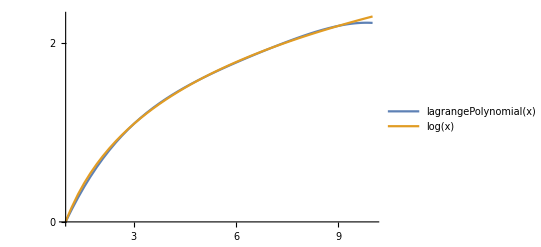

```mathematica
nodes={1,3,5,7,9};
values=N[Log[nodes]];
lagrangePolynomial[x_]=LagrangePolynomial[nodes,values];
Print["Lagrange Polynomial : ",Simplify[lagrangePolynomial[x]]];
Print[Plot[{lagrangePolynomial[x],Log[x]},{x,1,10},Ticks->{Range[0,10]},PlotLegends->"Expressions"]];
```

## TRAPEZOIDAL RULE

Q1 . Intergrate ∫_0^2 x^2 Sin[x]ⅆx using Trapezoidal rule with 5 subintervals

```mathematica
f[x_]:=x^2*Sin[x];
a=0;
b=2;
n=5;(*No of intervals*)
h=(b-a)/n;
Sol=h/2*(f[a]+2*Sum[f[i],{i,a+h,b-h,h}]+f[b]);
Print["\nSolution of the given integral is ", N[Sol]];
```

Solution of the given integral is 2.49642

Q2 . Integrate ∫_0^1 1/(1+x)ⅆx using Trapezoidal rule with 4 equal intervals

```mathematica
f[x_]:=1/(1+x);
a=0;
b=1;
n=4;
h=(b-a)/n;
Sol=h/2*(f[a]+2*Sum[f[i],{i,a+h,b-h,h}]+f[b]);
Print["\nSolution of the given integral is ",N[Sol]];
```

Solution of the given integral is 0.697024

Q3 . Integrate ∫_1^5 x^3ⅆx using Trapezoidal Rule taking n = 10 and calculate the absolute error in the approximation.

```mathematica
f[x_]=x^3;
a=1;
b=5;
n=10;
h=(b-a)/n;
Sol=h/2*(f[a]+2*Sum[f[i],{i,a+h,b-h,h}]+f[b]);
Print["\nSolution of the given integral is ",N[Sol]];
actual=Integrate[x^3,{x,1,5}];
Print["The absolute error is ",N[Abs[actual-Sol]]];
```

Solution of the given integral is 156.96

The absolute error is 0.96

## Simpson’s 1/3rd rule

Q. Calculate the integral : ∫_0^2 e^(-x^2)ⅆx using Simpson’s 1/3rd rule taking n=10

```mathematica
f[x_]:=Exp[-x^2];
a=0;
b=2;
n=10;
h=(b-a)/n;
oddSum= Sum[f[i],{i,a+h,b-h,2*h}];
evenSum= Sum[f[i],{i,a+2h,b-2h,2*h}];
sol=h/3*(f[a]+4*oddSum+2*evenSum+f[b]);
Print["\nValue of given integral using Simpson's method is ",N[sol]];
```

Value of given integral using Simpson's method is 0.882075

## ODE using Euler’ s Method

Q. Solve the initial value problem dy/dx=e^x/y, y (0) = 1 for y (1) using Euler' s method

```mathematica
x[0]=0;
y[0]=1;
a=0;
b=1;
n=10;
h=(b-a)/n;
f[x_,y_]:=Exp[x]/y;
x[j_]:=x[j-1]+h;
y[j_]:=y[j-1]+h*f[x[j-1],y[j-1]];
Print[Grid[Prepend[Table[{i,N[x[i],4],N[y[i],7]},{i,1,10}],{"j","x[j]","y[j]"}],Dividers->All]];
```

j | x[j] | y[j]
1 | 0.1 | 1.1
2 | 0.2 | 1.20047
3 | 0.3 | 1.302214
4 | 0.4 | 1.405873
5 | 0.5 | 1.511986
6 | 0.6 | 1.62103
7 | 0.7 | 1.733435
8 | 0.8 | 1.849606
9 | 0.9 | 1.969931
10 | 1. | 2.094788

## ODE using Modified Euler’s Method

Q. Solve the initial value problem dy/dx=x+y, y (0) = 1 for y (0.3) using Euler' s method

```mathematica
x[0]=0;
y[0]=1;
a=0;
b=0.3;
n=10;
h=(b-a)/n;
f[x_,y_]:=x+y;
x[j_]:=x[j-1]+h;
y[j_]:=y[j-1]+h*f[x[j-1]+h/2,y[j-1]+h/2*f[x[j-1],y[j-1]]];
Print[Grid[Prepend[Table[{j,N[x[j],4],N[y[j],7]},{j,1,10}],{"j","x[j]","y[j]"}],Dividers->All]];
```

j | x[j] | y[j]
1 | 0.03 | 1.0309
2 | 0.06 | 1.06365
3 | 0.09 | 1.09832
4 | 0.12 | 1.13495
5 | 0.15 | 1.17362
6 | 0.18 | 1.21437
7 | 0.21 | 1.25728
8 | 0.24 | 1.30241
9 | 0.27 | 1.34983
10 | 0.3 | 1.3996